# Coupled Cooperative Model

## Supporting Information Insights into chemically-fueled supramolecular polymers

Anastasiia Sharko, Dimitri Livitz, Serena De Piccoli1, Kyle J. M. Bishop, and Thomas M. Hermans

```mathematica
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
bigSize = 14;
smallSize=12;
thin =0.6;
```

## Sustained Oscillations

UNITS: All concentrations are scaled by the dissociation constant K=e^ε and time by (k_+K)^-1.

### Parameter values

```mathematica
nmax=200; (* maximum polymer size *)
tmax = 10; (* maximum time *)
kp=1; (* rate constant for assembly *)
ctot=10^4;(* total monomer concentration *)
nc=2; (* critical nucleus size *)
Kd=1; (* dissociation constant, K=e^ε *)
Kc=10^11; (* dissociation constant, Subscript[K, c]=e^Subscript[ε, c] *)
ka=1/5; (* rate constant for activation *)
kd1=0;  (* rate constant for monomer deactivation *)
kd2= 10^3;  (* rate constant for polymer end deactivation *)
kd3=1;  (* rate constant for polymer chain deactivation *)
```

We define the standard chemical potential.

```mathematica
Clear[μo,kn]
ε=Log[Kd];   (* bond energy *)
εc=Log[Kc]; (* nucleus bond energy *)
μo[n_]:=Piecewise[{{(n-1) εc,n≤nc},{(n-nc) ε+(nc-1)εc,n>nc}}]
kn[i_,j_]:=kp Exp[μo[i+j]-μo[i]-μo[j]]
```

### Solve Numerically

-Graphics-

```mathematica
nn =Table[n,{n,1,nmax}];
aa[t_]=Table[Subscript[a, n][t],{n,1,nmax}];

(* governing equations *)
rhs=Flatten[{
(* ḋ *)
-ka d[t]+kd1 Subscript[a, 1][t]+2 kd2 Sum[Subscript[a, j][t],{j,2,nmax}]+kd3 Sum[(j-2) Subscript[a, j][t],{j,3,nmax}],
(* Subscript[ȧ, 1] *)
ka d[t]-kd1 Subscript[a, 1][t] +2 kd2 Subscript[a, 2][t]+2kd3 Sum[Subscript[a, j][t],{j,3,nmax}]-2 kp Subscript[a, 1][t] Sum[Subscript[a, j][t] ,{j,1,nmax-1}]+2 Sum[kn[j,1]Subscript[a, j+1][t],{j,1,nmax-1}],
(* Subscript[ȧ, j] *)
Table[
-2kd2 (Subscript[a, n][t]-(1-KroneckerDelta[n,nmax])Subscript[a, n+1][t]) 
-kd3(n-2) Subscript[a, n][t] 
+2 kd3 Sum[Subscript[a, j+n+1][t],{j,1,nmax-n-1}]
-2 kp Subscript[a, n][t] Sum[Subscript[a, j][t],{j,1,nmax-n}]
+kp  Sum[Subscript[a, j][t]Subscript[a, n-j][t],{j,1,n-1}]
-Subscript[a, n][t] Sum[kn[j,n-j],{j,1,n-1}]
+2  Sum[kn[j,n]Subscript[a, j+n][t],{j,1,nmax-n}],
{n,2,nmax}]}];

eqns=Thread[Flatten[{d'[t],D[aa[t],t]}]==rhs];

(* initial conditions *)
initc=Flatten[{d[0]==ctot,Thread[aa[0]==0]}]; 

(* solution *)
sol=NDSolve[{eqns,initc},Flatten[{d,aa[t]}],{t,0,tmax},PrecisionGoal->20];
```

### Visualize Solution

#### Descriptors

```mathematica
dCalc[t_]=d[t]/.sol[[1]];
a1Calc[t_]=Subscript[a, 1][t]/.sol[[1]];
a2Calc[t_]=Subscript[a, 2][t]/.sol[[1]];
a3Calc[t_]=Subscript[a, 3][t]/.sol[[1]];
a4Calc[t_]=Subscript[a, 4][t]/.sol[[1]];
m1Calc[t_]=Sum[n Subscript[a, n][t]/.sol[[1]],{n,2,nmax}];
m0Calc[t_]=Sum[ Subscript[a, n][t]/.sol[[1]],{n,2,nmax}];
m2Calc[t_]=Sum[n^2 Subscript[a, n][t]/.sol[[1]],{n,2,nmax}];
```

#### Oscillation Period

```mathematica
T = tmax-t/.FindRoot[a1Calc[t]==a1Calc[tmax],{t,tmax-0.7}]
```

0.750805

#### Monomer Conservation

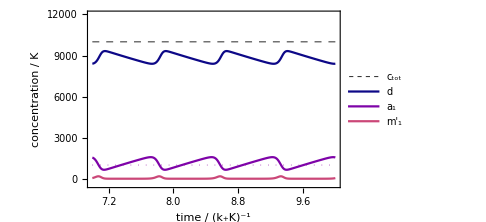

```mathematica
fig1=Plot[{dCalc[t]+a1Calc[t]+m1Calc[t],
dCalc[t],
a1Calc[t],
m1Calc[t],kd2},{t,tmax-3,tmax},
PlotRange->{-0.04 ctot, 1.2ctot},
ImageSize->360,
AspectRatio->1/GoldenRatio,
ImagePadding->{{70,10},{60,20}},
Frame->True,
PlotStyle->{
Directive[Black,Dashed,AbsoluteThickness[thin]],
Directive[MPLColorMap["Plasma"][0.0]],
Directive[MPLColorMap["Plasma"][0.25]],
Directive[MPLColorMap["Plasma"][0.5]],
Directive[Dotted,AbsoluteThickness[thin],MPLColorMap["Plasma"][0.3]]},
LabelStyle->{FontSize->smallSize,Black},
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameTicksStyle->Directive[Black,AbsoluteThickness[thin]],
PlotLegends->Placed[
LineLegend[{Style["c_tot",FontSize->smallSize],
Style["d",FontSize->smallSize],
Style["a_1",FontSize->smallSize],
Style["m'_1",FontSize->smallSize]},LegendMarkerSize->{20,2}] ,{0.9,0.44}],
FrameLabel->{Style["time / (k_+K)^-1",FontSize->bigSize],Style["concentration / K",FontSize->bigSize]}]
```

#### Limit Cycle

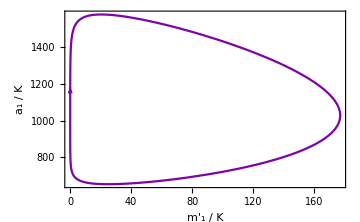

```mathematica
tStart=tmax-0.3;
tEnd=tStart+0.01;
limitCycle=ParametricPlot[{m1Calc[t],
a1Calc[t]},{t,tmax-T,tmax},
AspectRatio->1/GoldenRatio,
PlotRange->Full,
ImageSize->360,
ImagePadding->{{70,10},{60,20}},
Frame->True,
PlotStyle->{Directive[MPLColorMap["Plasma"][0.25]]},
LabelStyle->{FontSize->smallSize,Black},
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameTicksStyle->Directive[Black,AbsoluteThickness[thin]],
FrameLabel->{Style["m'_1 / K",FontSize->bigSize],Style["a_1 / K",FontSize->bigSize]},
Epilog->{MPLColorMap["Plasma"][0.25],Arrowheads[0.06],Arrow[{{m1Calc[tStart],a1Calc[tStart]},{m1Calc[tEnd],a1Calc[tEnd]}}]}]
```

#### Supporting Figure 11

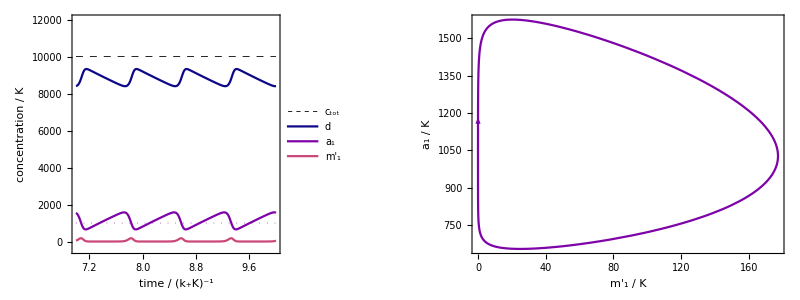

```mathematica
oscillations =Style[Grid[{{
Graphics[{
Inset[fig1],
Text[Style["a",FontSize->bigSize],Scaled[{-0.18,1.04}]]},
ImageSize->360,
ImagePadding->{{60,20},{60,20}},
AspectRatio->1/GoldenRatio],
Graphics[{
Inset[limitCycle],
Text[Style["b",FontSize->bigSize],Scaled[{-0.18,1.04}]]},
ImageSize->360,
ImagePadding->{{60,20},{60,20}},
AspectRatio->1/GoldenRatio]}}],
ImageSizeMultipliers->1]
```

```mathematica
(* Export[NotebookDirectory[]<>"oscillations.pdf", oscillations]*)
```

#### Polymer Moments

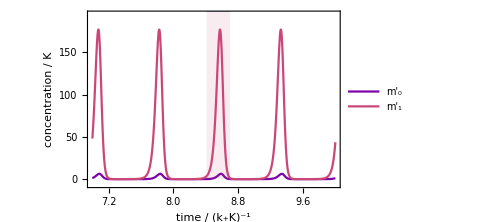

```mathematica
start=t/.FindRoot[m0Calc[t]==0.1,{t,8.3}];
finish=t/.FindRoot[m0Calc[t]==0.1,{t,8.7}];moments=Show[Plot[{m0Calc[t],m1Calc[t]},{t,tmax-3,tmax},
LabelStyle->Directive[Black,FontSize->smallSize],
FrameLabel->{
Style["time / (k_+K)^-1 ",FontSize->bigSize],
Style["concentration / K",FontSize->bigSize]},
PlotStyle->{Directive[MPLColorMap["Plasma"][0.25]],Directive[MPLColorMap["Plasma"][0.5]]},
PlotRange->3{-2,65},
ImageSize->360,
ImagePadding->{{60,20},{60,20}},
Frame->True,
PlotLegends->Placed[
LineLegend[{Style["m'_0",FontSize->smallSize],
Style["m'_1",FontSize->smallSize]},LegendMarkerSize->{20,2}] ,{0.9,0.44}],
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameTicksStyle->Directive[Black,AbsoluteThickness[thin]]],
Plot[200,{t,start,finish},Filling->Axis,FillingStyle->Directive[MPLColorMap["Plasma"][0.5],Opacity[0.1]]]]
```

#### Polymer Length

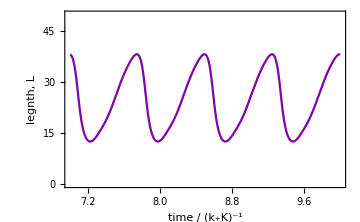

```mathematica
length=Plot[{m1Calc[t]/m0Calc[t]},{t,tmax-3,tmax},
LabelStyle->Directive[Black,FontSize->smallSize],
FrameLabel->{
Style["time / (k_+K)^-1 ",FontSize->bigSize],
Style["legnth, L",FontSize->bigSize]},
PlotStyle->{Directive[MPLColorMap["Plasma"][0.25]]},
PlotRange->{0,50},
ImageSize->360,
ImagePadding->{{60,20},{60,20}},
Frame->True,
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameTicksStyle->Directive[Black,AbsoluteThickness[thin]]]
```

#### Polymer Distributions (number basis)

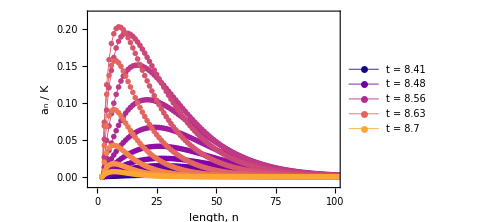

```mathematica
nCurves=17;
times=Table[time,{time,start,finish,(finish-start)/(nCurves-1)}];
dist=ListPlot[ Table[Transpose[{nn[[2;;]],aa[t][[2;;]]/.sol[[1]]/.t->time}],{time,start,finish,(finish-start)/(nCurves-1)}],
Frame->True,
LabelStyle->{FontSize->smallSize,Black},
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
Joined->True,
ImageSize->360,
PlotLegends->Placed[{
StringForm["t = ``",NumberForm[times[[1]],3]],None,None,None,
StringForm["t = ``",NumberForm[times[[5]],3]],None,None,None,
StringForm["t = ``",NumberForm[times[[9]],3]],None,None,None,
StringForm["t = ``",NumberForm[times[[13]],3]],None,None,None,
StringForm["t = ``",NumberForm[times[[17]],3]]},Scaled[{0.82,0.6}]],
ImagePadding->{{60,20},{60,20}},
PlotRange->{{-2,100},{-0.01,0.22}},
PlotStyle->Table[Directive[MPLColorMap["Plasma"][n],Opacity[1],AbsoluteThickness[thin]],{n,0,0.9,0.9/(nCurves+1)}],
PlotMarkers->{•},
FrameLabel->{
Style["length, n",FontSize->bigSize],
Style["a_n / K",FontSize->bigSize]}]
```

#### Limit Cycle

```mathematica
a1Max=FindMaximum[{a1Calc[t],t<tmax},{t,tmax-1}][[1]]
a1Min=FindMinimum[{a1Calc[t],t<tmax},{t,tmax-1}][[1]]
```

1575.6

654.691

```mathematica
Lmax=FindMaximum[{m1Calc[t]/m0Calc[t],t<tmax},{t,tmax-1}][[1]]
Lmin=FindMinimum[{m1Calc[t]/m0Calc[t],t<tmax},{t,tmax-1}][[1]]
```

38.2812

12.5745

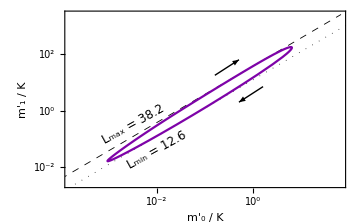

```mathematica
cycle=Show[
Plot[{logm0+Log10[Lmax],logm0+Log10[Lmin]},{logm0,-4,2},
Frame->True,
Axes->False,
ImageSize->360,
ImagePadding->{{60,20},{60,20}},
AspectRatio->1/GoldenRatio,
PlotRange->{{-3.8,1.8},{-2.6,3.4}},
PlotStyle->{
Directive[Black,Dashed,AbsoluteThickness[thin]],
Directive[Black,Dotted,AbsoluteThickness[thin]]},
LabelStyle->{FontSize->smallSize,Black},
FrameLabel->{
Style["m'_0 / K",FontSize->bigSize],
Style["m'_1 / K",FontSize->bigSize]},
FrameTicks->{
{Table[{i,Superscript[10,i]},{i,-2,3}],
Table[{i,""},{i,-2,3}]},
{Table[{i,Superscript[10,i]},{i,-4,2}],
Table[{i,""},{i,-4,2}]}},
FrameTicksStyle->Directive[Black,AbsoluteThickness[thin]],
Epilog->{Inset[Rotate[Style["L_max = 38.2",FontSize->smallSize],29 Degree],{-2.5,-0.5}],
Inset[Rotate[Style["L_min = 12.6",FontSize->smallSize],29 Degree],{-2,-1.4}],
Arrow[{{-0.3,0.3}+0.5{1,1.1},{-0.3,0.3}}],
Arrow[{{-0.3,1.8}-0.5{1,1.1},{-0.3,1.8}}]}],
ParametricPlot[{Log10[m0Calc[t]],Log10[m1Calc[t]]},{t,tmax-T,tmax},
PlotStyle->{Directive[MPLColorMap["Plasma"][0.25]]}]]
```

#### Supporting Figure 12

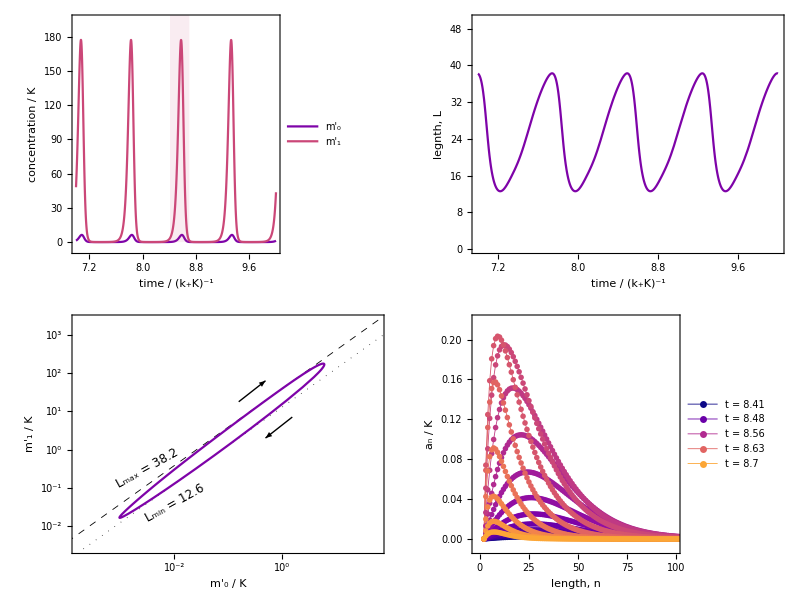

```mathematica
distribution =Style[Grid[{
{
Graphics[
{Inset[moments],
Text[Style["a",FontSize->bigSize],Scaled[{-0.18,1.04}]]},
ImageSize->360,
ImagePadding->{{60,20},{60,20}},
AspectRatio->1/GoldenRatio],
Graphics[
{Inset[length],
Text[Style["b",FontSize->bigSize],Scaled[{-0.18,1.04}]]},
ImageSize->360,
ImagePadding->{{60,20},{60,20}},
AspectRatio->1/GoldenRatio]
},
{
Graphics[
{Inset[cycle],
Text[Style["c",FontSize->bigSize],Scaled[{-0.18,1.04}]]},
ImageSize->360,
ImagePadding->{{60,20},{60,20}},
AspectRatio->1/GoldenRatio],
Graphics[
{Inset[dist],
Text[Style["d",FontSize->bigSize],Scaled[{-0.18,1.04}]]},
ImageSize->360,
ImagePadding->{{60,20},{60,20}},
AspectRatio->1/GoldenRatio]}}],ImageSizeMultipliers->1]
```

```mathematica
(* Export[NotebookDirectory[]<>"distribution.pdf",distribution] *)
```

#### Animated Distributions

```mathematica
tStart=t/.FindMinimum[{m1Calc[t],tmax/2<t<tmax},{t,tmax-2T}][[2]]
```

8.11318

```mathematica
plots=Table[ListPlot[ Transpose[{nn[[2;;]],nn[[2;;]]aa[t][[2;;]]/.sol[[1]]/.t->time}],
Frame->True,
Filling->Automatic,
PlotStyle->{MPLColorMap["Plasma"][0.2]},
PlotMarkers->{•},
AspectRatio->3.5/5,
ImageSize->350,
ImagePadding->{{60,20},{60,20}},
PlotRange->{{0,nmax},{0,4}},
LabelStyle->{FontSize->smallSize,Black},
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameLabel->{Style["length, n",FontSize->bigSize],Style["n a_n / K",FontSize->bigSize]}],{time,tStart,tStart+T,T/50}];
```

```mathematica
ListAnimate[plots]
```

```mathematica
(* Export[NotebookDirectory[]<>"polymer_oscillations.gif",plots,ImageResolution->300,"AnimationRepetitions"->∞] *)
```

#### Animated limit cycle

```mathematica
loop=ParametricPlot[{m1Calc[t],
a1Calc[t]},{t,tmax-T,tmax},PlotRange->Full,
ImageSize->350,
ImagePadding->{{60,20},{60,20}},
AspectRatio->5/5,
Frame->True,
PlotStyle->{Directive[MPLColorMap["Plasma"][0.25]]},
LabelStyle->{FontSize->smallSize,Black},
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameLabel->{Style["m'_1 / K",FontSize->bigSize],Style["a_1 / K",FontSize->bigSize]}];
```

```mathematica
plots=Table[Show[loop,
ListPlot[{{m1Calc[t],
a1Calc[t]}}/.t->time,
PlotStyle->Directive[MPLColorMap["Plasma"][0.25]],
PlotMarkers->{Automatic,Offset[10]}]],{time,tStart,tStart+T,T/50.}];
```

```mathematica
ListAnimate[plots]
```

```mathematica
(* Export[NotebookDirectory[]<>"roller_coaster.gif",plots,ImageResolution->300,"AnimationRepetitions"->∞] *)
```

## Moment Evolution

### Deactivated monomer d

-Graphics-

```mathematica
dRate[t_]=-ka dCalc[t]+kd1 a1Calc[t]+2 kd2 m0Calc[t]+kd3 (m1Calc[t]-2m0Calc[t]);
```

```mathematica
table[pairs_]:=Grid[pairs,Spacings->{0.5,-0.6},Alignment->{Left,Center}];
```

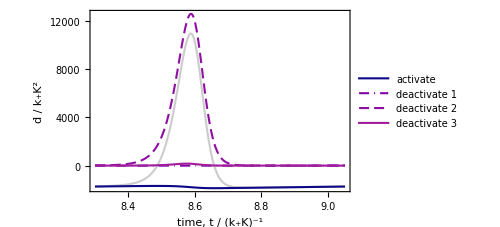

```mathematica
tStart=8.3;
dPlot=Plot[{
dRate[t],
-ka dCalc[t],
kd1 a1Calc[t],
2kd2 m0Calc[t],
kd3(m1Calc[t]-2m0Calc[t])},{t,tStart,tStart+T},
Frame->True,
PlotRange->Full,
ImageSize->370,
ImagePadding->{{70,20},{60,20}},
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameTicksStyle->Directive[Black,AbsoluteThickness[thin]],
PlotStyle->{
Directive[GrayLevel[0.8],AbsoluteThickness[1.5]],
Directive[MPLColorMap["Plasma"][0],AbsoluteThickness[1.5]],
Directive[Dashing[{0.02,0.01,0,0.01}],MPLColorMap["Plasma"][0.25],AbsoluteThickness[1.5]],
Directive[Dashing[{0.02,0.01}],MPLColorMap["Plasma"][0.30],AbsoluteThickness[1.5]],
Directive[MPLColorMap["Plasma"][0.35],AbsoluteThickness[1.5]]},
(*PlotLabels->Placed[{"test","test2"},Above],*)
PlotLegends->Placed[LineLegend[{
None,
"activate",
"deactivate 1",
"deactivate 2",
"deactivate 3"},
LegendMarkerSize->30,
LegendLayout->(Grid[##,Spacings->{.5,-1},Alignment->Left]&)],
Scaled[{0.76,0.62}]],
LabelStyle->{FontSize->smallSize,Black},
FrameLabel->{Style["time, t / (k_+K)^-1",FontSize->bigSize],
Style["ḋ / k_+K^2",FontSize->bigSize]}]
```

#### Derivation

-Graphics-

-Graphics-

∑_(j=2)^∞ a_j=m'_0

∑_(j=3)^∞ (j-2)a_j=∑_(j=2)^∞ (j-2)a_j-(2-2)a_2=m'_1-2 m'_0

### Activated free monomer a_1

-Graphics-

```mathematica
a1Rate[t_]=ka d[t]-kd1 Subscript[a, 1][t] +2 kd2 Subscript[a, 2][t]+2kd3 Sum[Subscript[a, j+2][t],{j,1,nmax-2}]-2 kp Subscript[a, 1][t] Sum[Subscript[a, j][t] ,{j,1,nmax-1}]+2 Sum[kn[j,1]Subscript[a, j+1][t],{j,1,nmax-1}]/.sol[[1]];
```

```mathematica
a1Rate[t_]=ka dCalc[t]-kd1 a1Calc[t]+2 kd2 a2Calc[t]+2 kd3(m0Calc[t]-a2Calc[t])-2 kp a1Calc[t]^2-2kp a1Calc[t] m0Calc[t]+2kp Kc a2Calc[t]+2kp Kd(m0Calc[t]-a2Calc[t]);
```

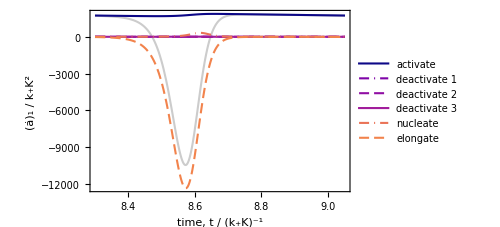

```mathematica
a1Plot=Plot[{a1Rate[t],
ka dCalc[t], (* activate *)
-kd1 a1Calc[t], (* deactivate 1 *)
+2kd2 a2Calc[t], (* deactivate 2 *)
+2 kd3(m0Calc[t]-a2Calc[t]), (* deactivate 3 *)
-2kp a1Calc[t]^2+2kp  Kc a2Calc[t], (* nucleate*)
-2kp a1Calc[t]m0Calc[t]+2kp Kd (m0Calc[t]-a2Calc[t]) (* elongate *)},
{t,tStart,tStart+T},
Frame->True,
PlotRange->Full,
ImageSize->370,
ImagePadding->{{70,20},{60,20}},
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameTicksStyle->Directive[Black,AbsoluteThickness[thin]],
PlotStyle->{
Directive[GrayLevel[0.8],AbsoluteThickness[1.5]],
Directive[MPLColorMap["Plasma"][0],AbsoluteThickness[1.5]],
Directive[Dashing[{0.02,0.01,0,0.01}],MPLColorMap["Plasma"][0.25],AbsoluteThickness[1.5]],
Directive[Dashing[{0.02,0.01}],MPLColorMap["Plasma"][0.30],AbsoluteThickness[1.5]],
Directive[MPLColorMap["Plasma"][0.35],AbsoluteThickness[1.5]],
Directive[Dashing[{0.02,0.01,0,0.01}],MPLColorMap["Plasma"][0.65],AbsoluteThickness[1.5]],
Directive[Dashing[{0.02,0.01}],MPLColorMap["Plasma"][0.70],AbsoluteThickness[1.5]]},
PlotLegends->Placed[LineLegend[{None,
"activate",
"deactivate 1",
"deactivate 2",
"deactivate 3",
"nucleate",
"elongate"},
LegendMarkerSize->30,
LegendLayout->(Grid[##,Spacings->{.5,-1},Alignment->Left]&)],
Scaled[{0.76,0.42}]],
LabelStyle->{FontSize->12,Black},
FrameLabel->{Style["time, t / (k_+K)^-1",FontSize->bigSize],
Style["(ȧ)_1 / k_+K^2",FontSize->bigSize]}]
```

#### Derivation

-Graphics-

-Graphics-

∑_(j=3)^∞ a_j=m'_0-a_2

∑_(j=1)^∞ a_j=a_1+m'_0

∑_(j=1)^∞ k_j1^-a_(j+1)=K_c a_2+K∑_(j=2)^∞ a_(j+1)=K_c a_2+K ∑_(j=3)^∞ a_j=K_c a_2+K (m'_0-a_2)

### Polymerized monomer m_1

-Graphics-

```mathematica
m1Rate[t_]=- 2kd2(a2Calc[t]+ m0Calc[t])- kd3 (m1Calc[t]-2a2Calc[t])+2kp(a1Calc[t]^2- Kc a2Calc[t])+2 kp a1Calc[t] m0Calc[t]- 2kp Kd(m0Calc[t]-a2Calc[t]);
```

```mathematica
m1Rate[5]+dRate[5]+a1Rate[5]
```

-3.00815×10^-10

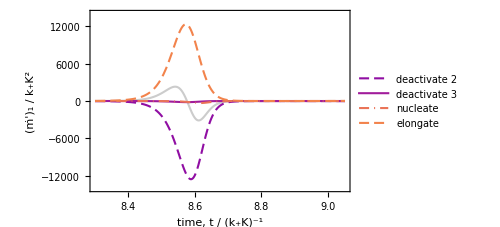

```mathematica
m1Plot=Plot[{m1Rate[t],
- 2kd2(a2Calc[t]+ m0Calc[t]),
- kd3 (m1Calc[t]-2a2Calc[t]),
2kp(a1Calc[t]^2- Kc a2Calc[t]),
2 kp a1Calc[t] m0Calc[t]- 2kp Kd(m0Calc[t]-a2Calc[t])
},{t,tStart,tStart+T},
Frame->True,
PlotRange->{-14000,14000},
ImageSize->370,
ImagePadding->{{70,20},{60,20}},
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameTicksStyle->Directive[Black,AbsoluteThickness[thin]],
PlotStyle->{Directive[GrayLevel[0.8],AbsoluteThickness[1.5]],
Directive[Dashing[{0.02,0.01}],MPLColorMap["Plasma"][0.3],AbsoluteThickness[1.5]],
Directive[MPLColorMap["Plasma"][0.35],AbsoluteThickness[1.5]],
Directive[Dashing[{0.02,0.01,0,0.01}],MPLColorMap["Plasma"][0.65],AbsoluteThickness[1.5]],
Directive[Dashing[{0.02,0.01}],MPLColorMap["Plasma"][0.70],AbsoluteThickness[1.5]]},
PlotLegends->Placed[LineLegend[{None,"deactivate 2","deactivate 3","nucleate","elongate"},
LegendMarkerSize->30,
LegendLayout->table],Scaled[{0.78,0.5}]],
LabelStyle->{FontSize->12,Black},
FrameLabel->{Style["time, t / (k_+K)^-1",FontSize->bigSize],
Style[" (ṁ')_1 / k_+K^2",FontSize->bigSize]}]
```

#### Derivation

-Graphics-

∑_(n=2)^∞ n a_n=m'_1

∑_(n=2)^∞ n a_(n+1)=∑_(n=3)^∞ (n-1)a_n=∑_(n=2)^∞ (n-1)a_n-(2-1)a_n=m'_1-m'_0-a_2

∑_(n=2)^∞ n (n-2) a_n=m'_2-2 m'_1

∑_(n=2)^∞ ∑_(j=2)^∞ n a_(j+n)=(2 a_4 | 2 a_5 | 2 a_6 | 2 a_7
3 a_5 | 3 a_6 | 3 a_7 | ⋯
4 a_6 | 4 a_7 | ⋯ | ⋯
5 a_7 | ⋯ | ⋯ | ⋯)
	=∑_(i=4)^∞ (∑_(k=2)^(i-2) k) a_i=1/2∑_(i=4)^∞ (-3 i+i^2) a_i=1/2∑_(i=2)^∞ (-3 i+i^2) a_i-1/2 (-3 2+2^2) a_2-1/2 (-3 3+3^2) a_3
	=1/2(-3 m'_1+m'_2)+ a_2

∑_(n=2)^∞ n a_n∑_(j=1)^∞ a_j=∑_(n=2)^∞ n a_n(m'_0+a_1)=(m'_0+a_1)m'_1

∑_(n=2)^∞ n∑_(j=1)^(n-1) a_j a_(n-j)=(. | . | . | .
2 a_1 a_1 | . | . | .
3 a_1 a_2 | 3 a_2 a_1 | . | .
4 a_1 a_3 | 4 a_2 a_2 | 4 a_3 a_1 | .)
	=∑_(j=1)^∞ ∑_(n=j+1)^∞ n a_j a_(n-j)=∑_(j=1)^∞ a_j∑_(n=j+1)^∞ n a_(n-j)=∑_(j=1)^∞ a_j∑_(k=1)^∞ (k+j) a_k
	=∑_(j=1)^∞ a_j(m_1+j m_0)=2 m_1 m_0=2(a_1+m'_1)(a_1+m'_0)

∑_(n=2)^∞ n a_n∑_(j=1)^(n-1) k_(j,n-j)^-=(. | . | . | .
2 a_2 k_(1,1)^- | . | . | .
3 a_3 k_(1,2)^- | 3 a_3 k_(2,1)^- | . | .
4 a_4 k_(1,3)^- | 4 a_4 k_(2,2)^- | 4 a_4 k_(3,1)^- | .
5 a_5 k_(1,4)^- | 5 a_5 k_(2,3)^- | 5 a_5 k_(3,2)^- | 5 a_5 k_(4,1)^-)=k_+(. | . | . | .
2 K_c a_2 | . | . | .
3 K a_3 | 3  K a_3 | . | .
4K a_4 | 4 K^2/K_c a_4 | 4K a_4 | .
5K a_5 | 5 K^2/K_c a_5 | 5 K^2/K_c a_5 | 5 K^2/K_c a_4)
	=k_+(2 K_c a_2+2K∑_(k=3)^∞ k a_k+K^2/K_c∑_(k=4)^∞ (k-3)k a_k)
	=k_+(2 K_c a_2+2K( m'_1-2 a_2)+K^2/K_c(∑_(k=2)^∞ (k-3)k a_k-(2-3)2 a_2))
	=k_+(2 K_c a_2+2K( m'_1-2 a_2)+K^2/K_c(m'_2-3 m'_1+2 a_2))

∑_(n=2)^∞ n ∑_(j=1)^∞ k_(j,n)^-a_(n+j)=(. | . | . | .
2 a_3 k_(1,2)^- | 2 a_4 k_(2,2)^- | 2 a_5 k_(3,2)^- | ⋯
3 a_4 k_(1,3)^- | 3 a_5 k_(2,3)^- | 3 a_6 k_(3,3)^- | ⋯
⋮ | ⋮ | ⋮ | ⋱)=k_+(. | . | . | .
2 K a_3 | 2 K^2/K_c a_4 | 2 K^2/K_c a_5 | ⋯
3 K a_4 | 3 K^2/K_c a_5 | 3 K^2/K_c a_6 | ⋯
⋮ | ⋮ | ⋮ | ⋱)
	=k_+(K∑_(k=2)^∞ k a_(k+1)+K^2/K_c∑_(k=4)^∞ (∑_(i=2)^(k-2) i)a_k)
	=k_+(K∑_(k=3)^∞ (k-1) a_k+K^2/(2 K_c)∑_(k=4)^∞ (-3 k+k^2)a_k)
	=k_+(K(∑_(k=2)^∞ (k-1) a_k-(2-1) a_2)+K^2/(2 K_c)(∑_(k=2)^∞ (-3 k+k^2)a_k- (-3 2+2^2)a_2- (-3 3+3^2)a_3))
	=k_+(K(m'_1-m'_0- a_2)+K^2/(2 K_c)(-3 m'_1+m'_2+2 a_2))

-Graphics-

(ṁ')_1=-2k'_d2(m'_1-m'_1-m'_0-a_2)-k'_d3(m'_2-2 m'_1)+2 k'_d3(1/2(-3 m'_1+m'_2)+ a_2)
	-2k_+(m'_0+a_1)m'_1+k_+2(a_1+m'_1)(a_1+m'_0)-k_+(2 K_c a_2+2K( m'_1-2 a_2)+K^2/K_c(m'_2-3 m'_1+2 a_2))
	+2 k_+K(m'_1-m'_0- a_2)+k_+K^2/(2 K_c)(-3 m'_1+m'_2+2 a_2)

(ṁ')_1=2k'_d2(m'_0+a_2)- k'_d3(m'_1-2 a_2)+2 k_+a_1^2-2 k_+K_c a_2+2 k_+a_1 m'_0-2 k_+K ( m'_0-2 a_2)

-Graphics-

### Polymer Chains, m'_0=∑_(j=2)^∞ a_j

-Graphics-

```mathematica
m0Rate[t_]=-2kd2 a2Calc[t]+kd3(m1Calc[t]-4m0Calc[t]+2a2Calc[t])+kp(a1Calc[t]^2-Kc a2Calc[t])-kp m0Calc[t]^2 +kp Kd^2/Kc(m1Calc[t]-3m0Calc[t]+a2Calc[t]);
```

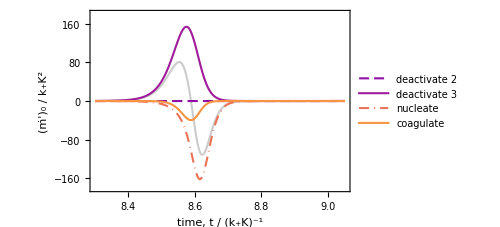

```mathematica
m0Plot=Plot[{m0Rate[t],
-2kd2 a2Calc[t],
kd3(m1Calc[t]-4m0Calc[t]+2a2Calc[t]),
kp(a1Calc[t]^2-Kc a2Calc[t]),
-kp m0Calc[t]^2 +kp Kd^2/Kc(m1Calc[t]-3m0Calc[t]+a2Calc[t])},{t,tStart,tStart+T},
Frame->True,
PlotRange->{-180,180},
ImageSize->370,
ImagePadding->{{70,20},{60,20}},
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameTicksStyle->Directive[Black,AbsoluteThickness[thin]],
PlotStyle->{Directive[GrayLevel[0.8],AbsoluteThickness[1.5]],
Directive[Dashing[{0.02,0.01}],MPLColorMap["Plasma"][0.3],AbsoluteThickness[1.5]],
Directive[MPLColorMap["Plasma"][0.35],AbsoluteThickness[1.5]],
Directive[Dashing[{0.02,0.01,0,0.01}],MPLColorMap["Plasma"][0.65],AbsoluteThickness[1.5]],
Directive[MPLColorMap["Plasma"][0.75],AbsoluteThickness[1.5]]},
PlotLegends->Placed[LineLegend[{None,"deactivate 2","deactivate 3","nucleate","coagulate"},
LegendMarkerSize->30,
LegendLayout->table],Scaled[{0.78,0.5}]],
LabelStyle->{FontSize->12,Black},
FrameLabel->{Style["time, t / (k_+K)^-1",FontSize->bigSize],
Style[" (ṁ')_0 / k_+K^2",FontSize->bigSize]}]
```

#### Derivation

-Graphics-

∑_(n=2)^∞ (a_n-a_(n+1))=m'_0-(m'_0-a_2)=a_2

∑_(n=2)^∞ (n-2)a_n=m'_1-2 m'_0

∑_(n=2)^∞ ∑_(j=1)^∞ a_(j+n+1)=(. | . | . | .
a_4 | a_5 | a_6 | ⋯
a_5 | a_6 | ⋯ | ⋯
a_6 | ⋯ | ⋯ | ⋯)
	=∑_(j=4)^∞ (j-3)a_j=m'_1-2 a_2-3 a_3-3(m'_0-a_2-a_3)=m'_1-3 m'_0+a_2

∑_(n=2)^∞ a_n(∑_(j=1)^∞ a_j)=(a_1+m'_0)m'_0

∑_(n=2)^∞ ∑_(j=1)^(n-1) a_j a_(n-j)=(. | . | . | .
a_1 a_1 | . | . | .
a_1 a_2 | a_2 a_1 | . | .
a_1 a_3 | a_2 a_2 | a_2 a_2 | a_3 a_1)
	=∑_(j=1)^∞ ∑_(n=j+1)^∞ a_j a_(n-j)=∑_(j=1)^∞ a_j∑_(n-j=1)^∞ a_(n-j)=(a_1+m'_0)^2

Note that k_ij^-=k_+Piecewise[{{K_c, i=1, j = 1}, {K, i=1,j>1}, {K^2/K_c, i>1,j>1}}]

∑_(n=2)^∞ ∑_(j=1)^(n-1) k_(j,n-j)^-a_n=k_+K_c(. | . | . | . | .
a_2 | . | . | . | .
0 | 0 | . | . | .
0 | 0 | 0 | . | .
0 | 0 | 0 | 0 | .)+k_+K(. | . | . | . | .
0 | . | . | . | .
a_3 | a_3 | . | . | .
a_4 | 0 | a_4 | . | .
a_5 | 0 | 0 | a_5 | .)+(k_+K^2)/K_c(. | . | . | . | .
0 | . | . | . | .
0 | 0 | . | . | .
0 | a_4 | 0 | . | .
0 | a_5 | a_5 | 0 | .)
	=k_+K_c a_2+2 k_+K(m'_0-a_2)+(k_+K^2)/K_c∑_(n=4)^∞ (n-3)a_n
	=k_+K_c a_2+2 k_+K(m'_0-a_2)+(k_+K^2)/K_c(m'_1-3 a_3-2 a_2-3(m'_0-a_3-a_2))
	=k_+K_c a_2+2 k_+K(m'_0-a_2)+(k_+K^2)/K_c(m'_1-3 m'_0+a_2)

∑_(n=2)^∞ ∑_(j=1)^∞ k_jn^-a_(j+n)=k_+K∑_(n=2)^∞ a_(1+n)+(k_+K^2)/K_c∑_(n=2)^∞ ∑_(j=2)^∞ a_(j+n)=k_+K(m'_0-a_2)+(k_+K^2)/K_c(m'_1-3 m'_0+ a_2)

k_+K∑_(n=2)^∞ a_(1+n)=k_+K(m'_0-a_2)

(k_+K^2)/K_c∑_(n=2)^∞ ∑_(j=2)^∞ a_(j+n)=(. | . | . | .
. | a_4 | a_5 | a_6
. | a_5 | a_6 | ⋯
. | a_6 | ⋯ | ⋯)
	=(k_+K^2)/K_c∑_(n=4)^∞ (n-3)a_n=(k_+K^2)/K_c(m'_1-3 a_3-2 a_2-3(m'_0-a_3- a_2))
	=(k_+K^2)/K_c(m'_1-3 m'_0+ a_2)

-Graphics-

(ṁ')_0=-2 k'_d2 a_2-k'_d3(m'_1-2 m'_0)+2k'_d3(m'_1-3 m'_0+a_2)-2k_+(a_1+m'_0)m'_0+(k_+(a_1+m'_0))^2
	-(k_+K_c a_2+2 k_+K(m'_0-a_2)+(k_+K^2)/K_c(m'_1-3 m'_0+a_2))+k_+K(m'_0-a_2)+(k_+K^2)/K_c(m'_1-3 m'_0+ a_2)

(ṁ')_0=-2 k'_d2 a_2+k'_d3(m'_1-4 m'_0+2 a_2)+k_+a_1^2-k_+K_c a_2-k_+m_0^(′2)+(k_+K^2)/K_c(m'_1-3 m'_0+ a_2)

-Graphics-

### Combined plot

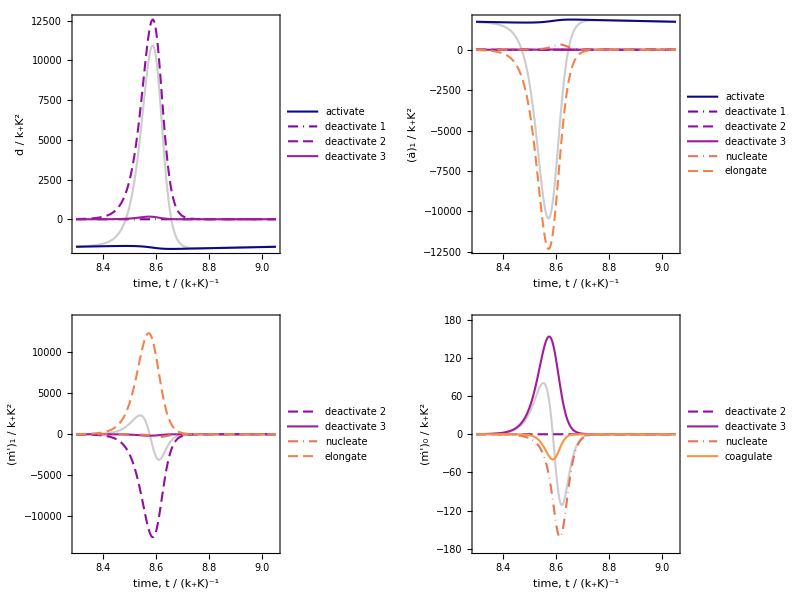

```mathematica
dominant=Style[Grid[{
{
Graphics[
{Inset[dPlot],
Text[Style["a",FontSize->bigSize],Scaled[{-0.18,1.04}]]},
ImageSize->370,
ImagePadding->{{70,20},{60,20}},
AspectRatio->1/GoldenRatio],
Graphics[
{Inset[a1Plot],
Text[Style["b",FontSize->bigSize],Scaled[{-0.18,1.04}]]},
ImageSize->370,
ImagePadding->{{70,20},{60,20}},
AspectRatio->1/GoldenRatio]
},
{
Graphics[
{Inset[m1Plot],
Text[Style["c",FontSize->bigSize],Scaled[{-0.18,1.04}]]},
ImageSize->370,
ImagePadding->{{70,20},{60,20}},
AspectRatio->1/GoldenRatio],
Graphics[
{Inset[m0Plot],
Text[Style["d",FontSize->bigSize],Scaled[{-0.18,1.04}]]},
ImageSize->370,
ImagePadding->{{70,20},{60,20}},
AspectRatio->1/GoldenRatio]}}],ImageSizeMultipliers->1]
```

```mathematica
(*Export[NotebookDirectory[]<>"dominant_terms.pdf",dominant]*)
```

### Dimers, a_2

-Graphics-

#### Derivation

-Graphics-

-Graphics-

∑_(j=2)^∞ a_(j+2)=∑_(j=4)^∞ a_j=m'_0-a_2-a_3

∑_(j=1)^∞ a_j=a_1+m'_0

∑_(j=1)^1 a_j a_(2-j)=a_1^2

∑_(j=1)^1 k_(j,2-j)^-=k_(1,1)^-=K_c

∑_(j=1)^∞ k_j2^-a_(j+2)=K a_3+K^2/K_c∑_(j=2)^∞ a_(j+2)=K a_3+K^2/K_c(m'_0-a_2-a_3)

## Simplified Model of Polymer Oscillations

### Closure

We approximate the polymer distribution as 

	a(n)≈m_0/(m_1/m_0-2)G((n-2)/(m_1/m_0-2))

The zeroth moment is 

	∫_2^∞ m_0/(m_1/m_0-2)G((n-2)/(m_1/m_0-2))ⅆn=∫_0^∞ m_0 G(x)ⅆx=m_0

where x=(n-2)/(m_1/m_0-2) and we have made use of the fact that ∫_0^∞ G(x)ⅆx=1. The first moment is 

	∫_2^∞ m_0/(m_1/m_2-2)n G((n-2)/(m_1/m_2-2))ⅆn=∫_0^∞ m_0((m_1/m_0-2)x+2)G(x)ⅆx
	=m_0(m_1/m_0-2)+2 m_0=m_1
	
where we have made use of the fact that ∫_0^∞ x G(x)ⅆx=1.

### Simple Model

The dominant contributions are 

	ḋ=-k_ad+2 k_d2 m'_0
	(ȧ)_1=k_a d-2 k_+ a_1 m'_0
	(ṁ')_1=-2 k'_d2 m'_0+2 k_+ a_1 m'_0
	(ṁ')_0=k'_d3(m_1-4 m_0)-F(a_1,m'_1,m'_0)

where F(a_1,m'_1,m'_0)=(2 k'_d2 C m'_0)/(m'_1/m'_0-2)^2+2 k'_d3 m'_0+k_+m_0^(′2)

```mathematica
Clear[m0,m1,a2]
sol2=NDSolve[{
d'[t]==-ka d[t]+ 2 kd2 m0[t] ,
a1'[t]==ka d[t] -2kp a1[t]m0[t],
m1'[t]==-2 kd2 m0[t]+2kp a1[t] m0[t] ,
m0'[t]==kd3 (m1[t]-4 m0[t])-  ((2 4.6kd2 m0[t])/(m1[t]/m0[t]-2)^2+2kd3 m0[t]+kp m0[t]^2),
d[0]==ctot,
a1[0]==1,
m1[0]==1,
m0[0]==1/30},{d[t],a1[t],m1[t],m0[t]},{t,0,10tmax},AccuracyGoal->60];
```

#### Period

```mathematica
f[t_?NumericQ]=a1[t]/.sol2[[1]];
10 tmax-t/.FindRoot[f[t]==f[10tmax],{t,10tmax-T}]
T
```

0.748123

0.750805

#### Monomer Conservation

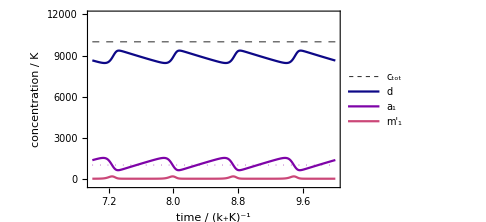

```mathematica
fig1Approx=Plot[{
ctot,
d[t]/.sol2[[1]]/.t->9 tmax+time,
a1[t]/.sol2[[1]]/.t->9 tmax+time,
m1[t]/.sol2[[1]]/.t->9 tmax+time,
kd2},{time,tmax-3,tmax},
PlotRange->{-0.04 ctot, 1.2ctot},
ImageSize->360,
AspectRatio->1/GoldenRatio,
ImagePadding->{{70,10},{60,20}},
Frame->True,
PlotStyle->{
Directive[Black,Dashed,AbsoluteThickness[thin]],
Directive[MPLColorMap["Plasma"][0.0]],
Directive[MPLColorMap["Plasma"][0.25]],
Directive[MPLColorMap["Plasma"][0.5]],
Directive[Dotted,AbsoluteThickness[thin],MPLColorMap["Plasma"][0.3]]},
LabelStyle->{FontSize->smallSize,Black},
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameTicksStyle->Directive[Black,AbsoluteThickness[thin]],
PlotLegends->Placed[
LineLegend[{Style["c_tot",FontSize->smallSize],
Style["d",FontSize->smallSize],
Style["a_1",FontSize->smallSize],
Style["m'_1",FontSize->smallSize]},LegendMarkerSize->{20,2}] ,{0.9,0.44}],
FrameLabel->{Style["time / (k_+K)^-1",FontSize->bigSize],Style["concentration / K",FontSize->bigSize]}]
```

#### Unstable Fixed Point

```mathematica
solFP=Quiet[Solve[{ctot==d+a1+m1 ,
0==ka d  -2kp a1 m0,
0==-2 kd2 m0+2kp a1 m0 ,
0==kd3 (m1-4 m0)-  ((2 4.6kd2 m0)/(m1/m0-2)^2+2kd3 m0+kp m0^2)},{d,a1,m1,m0}][[2]]]
m1/m0/.solFP
```

{d→8977.81,a1→1000.,m1→22.1933,m0→0.897781}

24.7201

Positive eigenvalues.

```mathematica
JacFP=Grad[{ka (ctot-a1-m1) -2kp a1 m0,
-2 kd2 m0+2kp a1 m0 ,
kd3 (m1-4 m0)-  ((2 4.6kd2 m0)/(m1/m0-2)^2+2kd3 m0+kp m0^2)},{a1,m1,m0}]/.solFP;
Eigenvalues[JacFP]
```

{-66.5477+0. ⅈ,0.075865+11.7884 ⅈ,0.075865-11.7884 ⅈ}

#### Limit Cycle

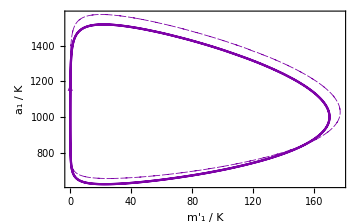

```mathematica
tStart=tmax-0.3;
tEnd=tStart+0.01;
limitCycleApprox=ParametricPlot[{{m1Calc[time],
a1Calc[time]},{m1[t],
a1[t]}/.sol2[[1]]/.t->9tmax+time},{time,tmax-2T,tmax},
AspectRatio->1/GoldenRatio,
PlotRange->Full,
ImageSize->360,
ImagePadding->{{70,10},{60,20}},
Frame->True,
PlotStyle->{Directive[Dashed,AbsoluteThickness[thin],MPLColorMap["Plasma"][0.25]],
Directive[MPLColorMap["Plasma"][0.25]]},
LabelStyle->{FontSize->smallSize,Black},
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameTicksStyle->Directive[Black,AbsoluteThickness[thin]],
FrameLabel->{Style["m'_1 / K",FontSize->bigSize],Style["a_1 / K",FontSize->bigSize]},
Epilog->{MPLColorMap["Plasma"][0.25],Arrowheads[0.06],Arrow[{{m1Calc[tStart],a1Calc[tStart]},{m1Calc[tEnd],a1Calc[tEnd]}}]}]
```

#### Combined Figure

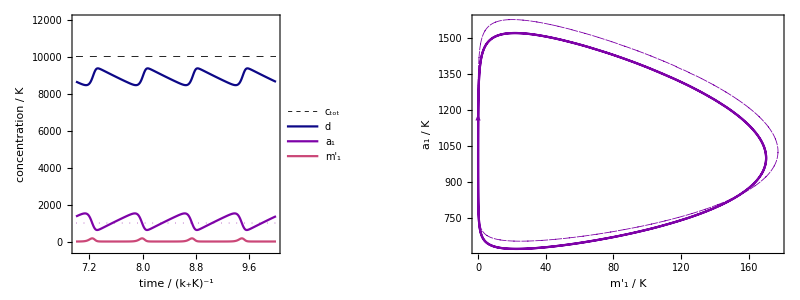

```mathematica
oscillations =Style[Grid[{{
Graphics[{
Inset[fig1Approx],
Text[Style["a",FontSize->bigSize],Scaled[{-0.18,1.04}]]},
ImageSize->360,
ImagePadding->{{60,20},{60,20}},
AspectRatio->1/GoldenRatio],
Graphics[{
Inset[limitCycleApprox],
Text[Style["b",FontSize->bigSize],Scaled[{-0.18,1.04}]]},
ImageSize->360,
ImagePadding->{{60,20},{60,20}},
AspectRatio->1/GoldenRatio]}}],
ImageSizeMultipliers->1]
```

```mathematica
(* Export[NotebookDirectory[]<>"oscillations_approx.pdf",oscillations]*)
```

### The approximate dynamics ensures physical solutions

The approximate dynamics on a_1, d, m'_0, m'_1 should ensure non-negative concentrations satisfying the following constraints 

	0<a_1<c_tot
	0<d<c_tot
	0<2 m'_0<m'_1<c_tot

where d+a_1+m_1=c_tot.  The solution space (a_1,m'_1,m'_0) is constrained within the tetrahedral region visualized below. To maintain physical solutions, the inward flux at any point on each face must be non-negative.

```mathematica
RegionPlot3D[(0≤a1≤1)&&(0≤2 m0≤m1≤1)&&(0≤m1+a1≤1),{a1,0,1},{m1,0,1},{m0,0,1},PlotPoints->50,
AxesLabel->{"a1","m1","m0"}]
```

-Graphics3D-

#### Face 1: a_1=0

For the face  a_1=0, the inward flux is (ȧ)_1=k_a d≥0, which is true.

#### Face 2: m'_0=0

For the face m'_0=0, the inward flux is (ṁ')_0=k_d3 m'_1-F(a_1,m'_1,0)≥0, which implies that 

	F(a_1,m'_1,0)≤k'_d3 m'_1
	F(a_1,m'_1,0)=0≤k'_d3 m'_1

which is true.

#### Face 3: a_1+m'_1=c_tot such that d=0

For the face a_1+m'_1=c_tot, the inward pointing normal vector is 

	 n=(-1,-1,0)

The inward flux is 

	-(ȧ)_1-(ṁ')_1=-(k_a d-2 k_+ a_1 m'_0)-(-2 k'_d2 m'_0+2 k_+ a_1 m'_0)≥0
	-(ȧ)_1-(ṁ')_1=2 k'_d2 m'_0≥0
	
which is true.

#### Face 4: 2 m'_0=m'_1

For the face -m'_1+2 m'_0=0, the inward pointing normal vector is 

	 n=(0,1,-2)

The inward flux is 

	(ṁ')_1-2(ṁ')_0=(-2 k'_d2 m'_0+2 k_+ a_1 m'_0)-2(k'_d3(m'_1-4 m'_0)-F(a_1,m'_1,m'_0))≥0
	(ṁ')_1-2(ṁ')_0=(-2 k'_d2 m'_0+2 k_+ a_1 m'_0)-2(k'_d3(2 m'_0-4 m'_0)-F(a_1,2 m'_0,m'_0))≥0
	F(a_1,2 m'_0,m'_0)≥(k'_d2-k_+ a_1-k'_d3)m'_0

and F(a_1,m'_1,m'_0)→∞ as m'_1→2 m_0 so this condition is also satisfied.

### Linearized Dynamics for Autocatalytic Growth

For a specified monomer concentration, the approximate dynamics is

	(ṁ')_1=-2 k'_d2 m'_0+2 k_+ a_1 m'_0
	(ṁ')_0=k'_d3(m'_1-4 m'_0)-(2 k'_d2 C)/(L-2)^2 m'_0-2 k_d3 m'_0-k_+m_0^(′2)

where L=m'_1/m'_0 is the mean length.  For long polymers, we can neglect the term (2 k'_d2 C)/(L-2)^2 m'_0

	6 k'_d3≫(2 k'_d2 C)/(L-2)^2  or L≫2+√((k'_d2 C)/(3 k'_d3)) 

The approximate linearized equations become

	((ṁ')_1
(ṁ')_0)=(0 | 2 k_+a_1-2 k_d2
k_d3 | -6 k_d3)(m'_1
m'_0)

```mathematica
J={{0,-2 kd2v+2kpv a1},
{kd3v,-6 kd3v}};
FullSimplify[Eigenvalues[J]]
```

{-3 kd3v-√(kd3v (-2 kd2v+9 kd3v+2 a1 kpv)),-3 kd3v+√(kd3v (-2 kd2v+9 kd3v+2 a1 kpv))}

```mathematica
Solve[-3 kd3v+√(kd3v (-2 kd2v+9 kd3v+2 a1 kpv))==0,a1]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{a1→kd2v/kpv}}

```mathematica
FullSimplify[Eigenvectors[J],Assumptions->kd3v>0]
```

{{3-√((-2 kd2v+9 kd3v+2 a1 kpv)/kd3v),1},{3+√((-2 kd2v+9 kd3v+2 a1 kpv)/kd3v),1}}

## Autocatalysis in Polymer Growth and Division

### Linearized equations about a_(n≥2)=0

Linearizing the rate equations about a_n=0, we obtain

	(ȧ)_2=-2k_d2(a_2-a_3)+2 k_d3 ∑_(j=1)^∞ a_(j+3)-2 k_+a_1 a_2+k_+a_1^2-k_+K_c a_2+2 k_+K a_3
	(ȧ)_n=-2k_d2(a_n-a_(n+1))-k_d3 (n-2)a_n+2 k_d3 ∑_(j=1)^∞ a_(j+n+1)-2 k_+a_1(a_n-a_(n-1))-2 k_+K a_n+2 k_+K a_(n+1)

These equations define the shape of the growing distribution.

#### Numerical Jacobian

```mathematica
J=Grad[Table[
-2kd2 (Subscript[a, n][t]-(1-KroneckerDelta[n,nmax])Subscript[a, n+1][t]) 
-kd3(n-2) Subscript[a, n][t] 
+2 kd3 Sum[Subscript[a, j+n+1][t],{j,1,nmax-n-1}]
-2 kp Subscript[a, n][t] Sum[Subscript[a, j][t],{j,1,nmax-n}]
+kp  Sum[Subscript[a, j][t]Subscript[a, n-j][t],{j,1,n-1}]
-Subscript[a, n][t] Sum[kn[j,n-j],{j,1,n-1}]
+2  Sum[kn[j,n]Subscript[a, j+n][t],{j,1,nmax-n}],
{n,2,nmax}],aa[t][[2;;]]]/.Thread[aa[t][[2;;]]->0];
```

#### Eigenvalues

```mathematica
Lambda1[a1_?NumericQ]:=Eigenvalues[N[J/.Subscript[a, 1][t]->a1],-1,Method->{"Automatic","Criteria"->"RealPart"}][[1]];
Lambda2[a1_?NumericQ]:=Eigenvalues[N[J/.Subscript[a, 1][t]->a1],-2,Method->{"Automatic","Criteria"->"RealPart"}][[1]];
```

```mathematica
Lambda1Data=Table[{a1,Re[Lambda1[a1]]},{a1,1.,2000.,2000/100.}];
Lambda2Data=Table[{a1,Re[Lambda2[a1]]},{a1,1.,2000.,2000/100.}];
```

```mathematica
a1Zero=a1/.FindRoot[Interpolation[Lambda1Data,a1],{a1,1000}]
```

1027.46

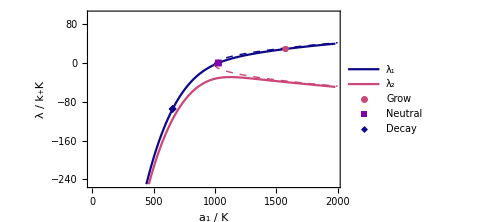

```mathematica
valPlot=Show[
ListLinePlot[{Lambda1Data,Lambda2Data},
Frame->True,
ImageSize->360,
PlotRange->{-250,100},
ImagePadding->{{60,20},{60,20}},
AspectRatio->1/GoldenRatio,
PlotStyle->{MPLColorMap["Plasma"][0],MPLColorMap["Plasma"][0.5]},
LabelStyle->{FontSize->smallSize,Black},
FrameLabel->{
Style["a_1 / K",FontSize->bigSize],
Style["λ / k_+K",FontSize->bigSize]},
PlotLegends->Placed[{"λ_1","λ_2"},{0.15,0.7}]],

Plot[(*{1/2 (-7 kd3+√kd3 √(-8 kd2+9 kd3+8 a1 kp)),1/2 (-7 kd3-√kd3 √(-8 kd2+9 kd3+8 a1 kp))}*)
{-3 kd3+√(kd3 (-2 kd2+9 kd3+2 a1 kp)),-3 kd3-√(kd3 (-2 kd2+9 kd3+2 a1 kp))},
(*{-2 kd3+√2 √(kd3 (-kd2+2 kd3+a1 kp)),-2 kd3-√2 √(kd3 (-kd2+2 kd3+a1 kp))}*){a1,0,2000},
PlotStyle->{Directive[MPLColorMap["Plasma"][0],Dashed,AbsoluteThickness[1]],
Directive[MPLColorMap["Plasma"][0.5],Dashed,AbsoluteThickness[1]]}],

ListPlot[{{{a1Max,Interpolation[Lambda1Data,a1Max]}},
{{a1Zero,Interpolation[Lambda1Data,a1Zero]}},
{{a1Min,Interpolation[Lambda1Data,a1Min]}}},
PlotMarkers->Automatic,
PlotStyle->{
MPLColorMap["Plasma"][0.5],
MPLColorMap["Plasma"][0.25],
MPLColorMap["Plasma"][0.0]},
PlotLegends->Placed[{
Style["Grow",FontSize->smallSize],
Style["Neutral",FontSize->smallSize],
Style["Decay",FontSize->smallSize]},{0.85,0.25}]
]
]
```

#### Eigenvectors

```mathematica
{valGrow,vecGrow}=Eigensystem[J/.Subscript[a, 1][t]->a1Max,-1,Method->{"Automatic","Criteria"->"RealPart"}];
{valDecay,vecDecay}=Eigensystem[J/.Subscript[a, 1][t]->a1Min,-1,Method->{"Automatic","Criteria"->"RealPart"}];
{valZero,vecZero}=Eigensystem[J/.Subscript[a, 1][t]->a1Zero,-1,Method->{"Automatic","Criteria"->"RealPart"}];
Re[valGrow[[1]]]
Re[valZero[[1]]]
Re[valDecay[[1]]]
```

28.9004

-0.0000358595

-94.789

```mathematica
Total[Re[vecGrow[[1]]]^2]
Total[Re[ vecZero[[1]]]^2]
Total[Re[ vecDecay[[1]]]^2]
```

1.

1.

1.

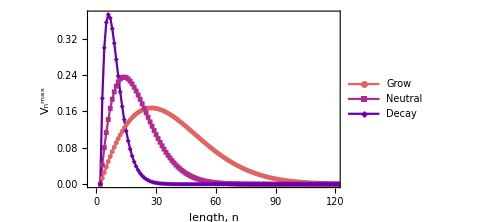

```mathematica
vecPlot=ListPlot[{
Transpose[{nn[[2;;]],Abs[Re[vecGrow[[1,All]]]]}],
Transpose[{nn[[2;;]],Abs[Re[vecZero[[1,All]]]]}],
Transpose[{nn[[2;;]],Abs[Re[vecDecay[[1,All]]]]}]},
PlotStyle->{
MPLColorMap["Plasma"][0.6],
MPLColorMap["Plasma"][0.4],
MPLColorMap["Plasma"][0.2]},
Joined->True,
PlotLegends->Placed[{"Grow","Neutral","Decay"},{0.8,0.7}],
PlotMarkers->{Automatic,5},
Frame->True,
ImageSize->360,
PlotRange->{{-2,120},Full},
ImagePadding->{{60,20},{60,20}},
AspectRatio->1/GoldenRatio,
PlotStyle->{MPLColorMap["Plasma"][0]},
LabelStyle->{FontSize->smallSize,Black},
FrameLabel->{
Style["length, n",FontSize->bigSize],
Style["V_n^max",FontSize->bigSize]}]
```

```mathematica
eigen =Style[Grid[{{Graphics[
{Inset[valPlot],
Text[Style["a",FontSize->bigSize],Scaled[{-0.18,1.04}]]},
ImageSize->360,
ImagePadding->{{60,20},{60,20}},
AspectRatio->1/GoldenRatio],
Graphics[
{Inset[vecPlot],
Text[Style["b",FontSize->bigSize],Scaled[{-0.18,1.04}]]},
ImageSize->360,
ImagePadding->{{60,20},{60,20}},
AspectRatio->1/GoldenRatio],}}],ImageSizeMultipliers->1]
```

-Graphics- | -Graphics- |

```mathematica
(* Export[NotebookDirectory[]<>"Eigen.pdf",eigen]*)
```